## Functions

```mathematica
<<PajaroLocoPublic`
PlotPopulationDynamicsFemales[data_]:=ListLinePlot[Append[Transpose[data],Total/@data]
,Frame->True
,FrameStyle->Thick
,PlotRange->{0,600}
,ImageSize->500
,PlotStyle->Directive[Thickness[.0075]]
]
PlotPopulationDynamicsMales[data_]:=ListLinePlot[Append[Transpose[data],Total/@data]
,Frame->True
,FrameStyle->Thick
,PlotRange->{{0,750},{0,2000}}
,PlotStyle->Thickness[.005]
,ImageSize->500
,PlotStyle->Directive[Thickness[.0075]]
]
StyleLabel[text_]:=Style[text,25]
```

## Lonely World

```mathematica
(*matrix={{1}};
edgeshape[e_,___]:={Arrowheads[{{.034,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{{{1}},{"1"}},1,VertexLabelStyle->.001,ImageSize->2000,VertexStyle->Directive[White,EdgeForm[Directive[Thickness[.02],Black]]],VariableStyle->"Both",EdgeShapeFunction->edgeshape];
Export["Graph.png",%,ImageSize->2000,ImageResolution->250]*)
```

Graph.png

## UDMel

```mathematica
SetDirectory[NotebookDirectory[]];
fileNames=FileNames["*.csv",Directory[]<>"/DARPAScenariosUDMel"];
labels=Import[fileNames[[1]]][[1,2;;All]];
rawData=(Import[#][[2;;All,2;;All]]&)/@fileNames;
Transpose[{fileNames}]//Grid;
fplot=PlotPopulationDynamicsFemales[rawData[[1]]];
colors=Cases[fplot,{___,c_Directive,__Line}:>ColorConvert[c,RGBColor],Infinity];
colorSwatch=SwatchLegend[colors,labels,LabelStyle->25,LegendMarkerSize->{{30,30}},LegendMarkers->"Bubble"];
```

```mathematica
plotsGridFemale=Grid[{
{"",StyleLabel["08"],StyleLabel["20"]},
{StyleLabel["02"],PlotPopulationDynamicsFemales[rawData[[1]]],PlotPopulationDynamicsFemales[rawData[[2]]]},
{StyleLabel["03"],PlotPopulationDynamicsFemales[rawData[[3]]],PlotPopulationDynamicsFemales[rawData[[4]]]},
{StyleLabel["04"],PlotPopulationDynamicsFemales[rawData[[5]]],PlotPopulationDynamicsFemales[rawData[[6]]]}
}];
plotsGridMale=Grid[{
{"",StyleLabel["08"],StyleLabel["20"]},
{StyleLabel["02"],PlotPopulationDynamicsMales[rawData[[7]]],PlotPopulationDynamicsMales[rawData[[8]]]},
{StyleLabel["03"],PlotPopulationDynamicsMales[rawData[[9]]],PlotPopulationDynamicsMales[rawData[[10]]]},
{StyleLabel["04"],PlotPopulationDynamicsMales[rawData[[11]]],PlotPopulationDynamicsMales[rawData[[12]]]}
}];
femaleGrid=Grid[{
{"",Style["Males",30],"",Style["Females",30],""},
{"",Style["Releases Interval",30],"",Style["Releases Interval",30],""},
{Style["Releases Number",30]//Rotate[#,90Degree]&,plotsGridMale,Style["Releases Number",30]//Rotate[#,90Degree]&,plotsGridFemale,colorSwatch}
}
,Background->{{LightBlue,None,LightBlue,None},{LightPurple,LightBlue}}
,Frame->True
,FrameStyle->Thick
];
```

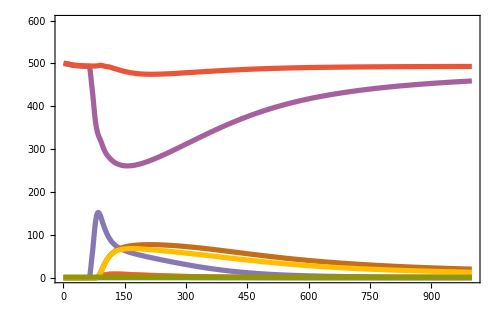
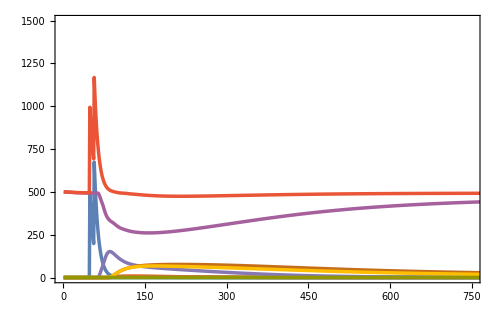
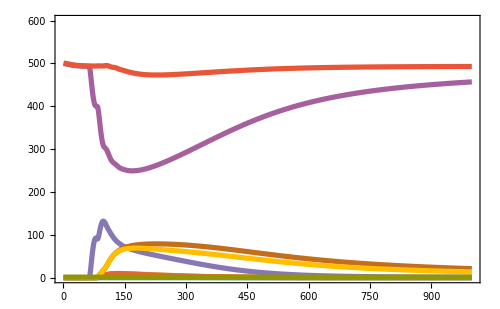
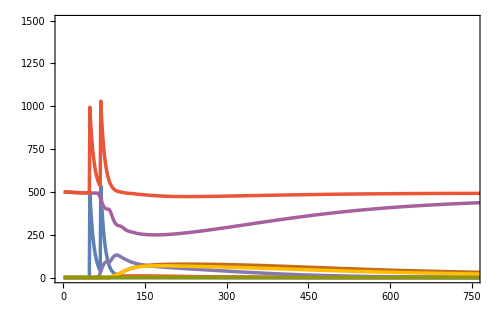
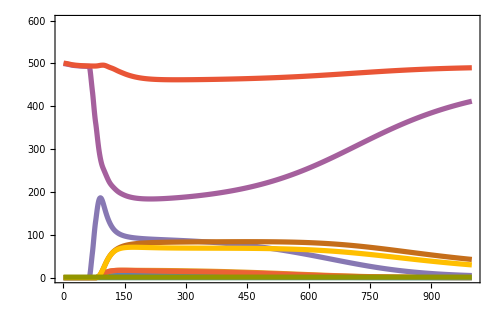
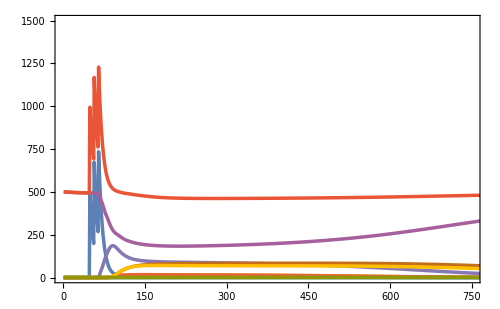
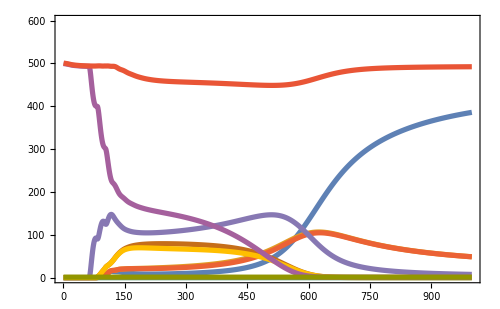
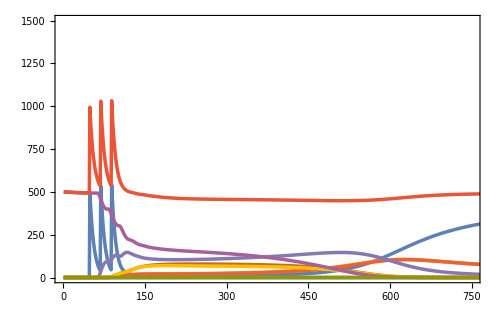
UDMel | 
 | 
 | 
 | Release Interval
Releases Number |  | 08 |  |  | 20 |  | 
02 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
03 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
04 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
 | F | M |  | F | M |  |

UDMel.png

```mathematica
plotsGridFull={
{"",StyleLabel["08"],StyleLabel[""],"",StyleLabel["20"],StyleLabel[""],""},
{StyleLabel["02"],PlotPopulationDynamicsFemales[rawData[[1]]],PlotPopulationDynamicsMales[rawData[[7]]],"   ",PlotPopulationDynamicsFemales[rawData[[2]]],PlotPopulationDynamicsMales[rawData[[8]]],"   "},
{StyleLabel["03"],PlotPopulationDynamicsFemales[rawData[[3]]],PlotPopulationDynamicsMales[rawData[[9]]],"   ",PlotPopulationDynamicsFemales[rawData[[4]]],PlotPopulationDynamicsMales[rawData[[10]]],"   "},
{StyleLabel["04"],PlotPopulationDynamicsFemales[rawData[[5]]],PlotPopulationDynamicsMales[rawData[[11]]],"   ",PlotPopulationDynamicsFemales[rawData[[6]]],PlotPopulationDynamicsMales[rawData[[12]]],"   "},
{"",StyleLabel["F"],StyleLabel["M"],"",StyleLabel["F"],StyleLabel["M"]}
}//Grid[#,Background->{{LightBlue,None,None,LightBlue,None,None,LightBlue},{LightBlue,None,None,None,LightPurple}}]&;
finalGrid=Grid[{
{"",Style["Release Interval",50]},
{Style["Releases Number",50]//Rotate[#,90Degree]&,plotsGridFull}
}
,Background->{{LightRed,None,LightRed,None},{LightRed,None,LightRed}}
]//Grid[{{Style["UDMel",100]},{},{},{#,colorSwatch}}]&
Export["UDMel.png",finalGrid,ImageResolution->200]
```

## Translocations

```mathematica
SetDirectory[NotebookDirectory[]];
fileNames=FileNames["*.csv",Directory[]<>"/DARPAScenariosTranslocations"];
labels=Import[fileNames[[1]]][[1,2;;All]];
rawData=(Import[#][[2;;All,2;;All]]&)/@fileNames;
Transpose[{fileNames}]//Grid;
fplot=PlotPopulationDynamicsFemales[rawData[[1]]];
colors=Cases[fplot,{___,c_Directive,__Line}:>ColorConvert[c,RGBColor],Infinity];
colorSwatch=SwatchLegend[colors,labels,LabelStyle->25,LegendMarkerSize->{{30,30}},LegendMarkers->"Bubble"];
```

```mathematica
plotsGridFemale=Grid[{
{"",StyleLabel["08"],StyleLabel["20"]},
{StyleLabel["02"],PlotPopulationDynamicsFemales[rawData[[1]]],PlotPopulationDynamicsFemales[rawData[[2]]]},
{StyleLabel["03"],PlotPopulationDynamicsFemales[rawData[[3]]],PlotPopulationDynamicsFemales[rawData[[4]]]},
{StyleLabel["04"],PlotPopulationDynamicsFemales[rawData[[5]]],PlotPopulationDynamicsFemales[rawData[[6]]]}
}];
plotsGridMale=Grid[{
{"",StyleLabel["08"],StyleLabel["20"]},
{StyleLabel["02"],PlotPopulationDynamicsMales[rawData[[7]]],PlotPopulationDynamicsMales[rawData[[8]]]},
{StyleLabel["03"],PlotPopulationDynamicsMales[rawData[[9]]],PlotPopulationDynamicsMales[rawData[[10]]]},
{StyleLabel["04"],PlotPopulationDynamicsMales[rawData[[11]]],PlotPopulationDynamicsMales[rawData[[12]]]}
}];
femaleGrid=Grid[{
{"",Style["Males",30],"",Style["Females",30],""},
{"",Style["Releases Interval",30],"",Style["Releases Interval",30],""},
{Style["Releases Number",30]//Rotate[#,90Degree]&,plotsGridMale,Style["Releases Number",30]//Rotate[#,90Degree]&,plotsGridFemale,colorSwatch}
}
,Background->{{LightBlue,None,LightBlue,None},{LightPurple,LightBlue}}
,Frame->True
,FrameStyle->Thick
];
```

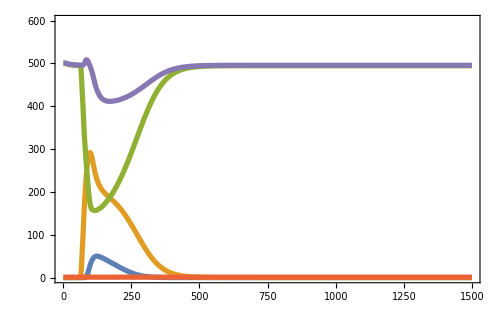
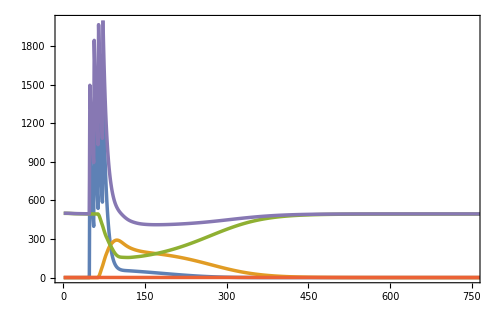
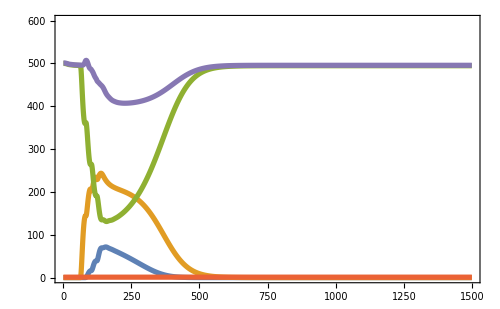
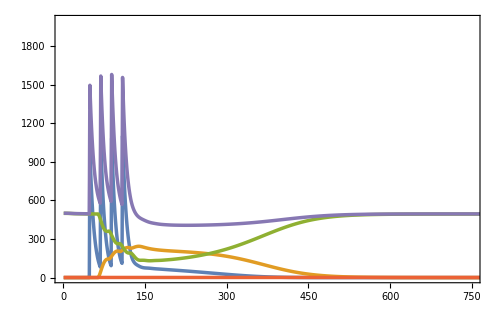
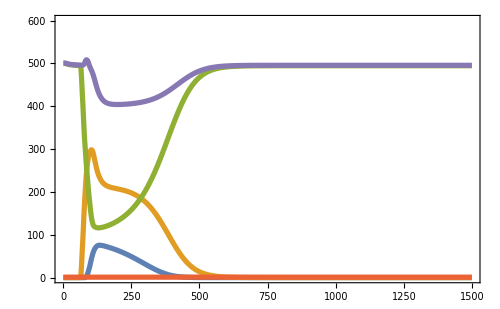
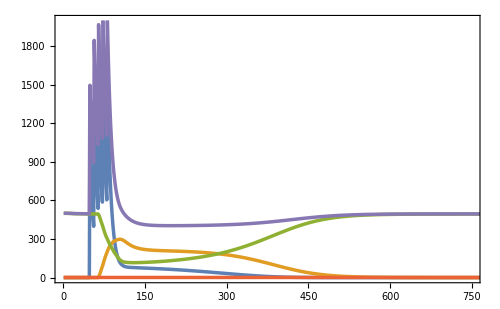
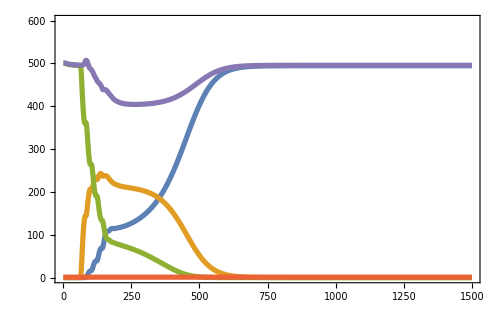
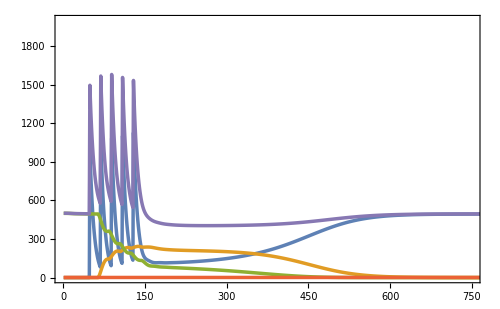
Translocations | 
 | 
 | 
 | Release Interval
Releases Number |  | 08 |  |  | 20 |  | 
02 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
03 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
04 | -Graphics- | -Graphics- |     | -Graphics- | -Graphics- |    
 | F | M |  | F | M |  |

Translocations.png

```mathematica
plotsGridFull={
{"",StyleLabel["08"],StyleLabel[""],"",StyleLabel["20"],StyleLabel[""],""},
{StyleLabel["02"],PlotPopulationDynamicsFemales[rawData[[1]]],PlotPopulationDynamicsMales[rawData[[7]]],"   ",PlotPopulationDynamicsFemales[rawData[[2]]],PlotPopulationDynamicsMales[rawData[[8]]],"   "},
{StyleLabel["03"],PlotPopulationDynamicsFemales[rawData[[3]]],PlotPopulationDynamicsMales[rawData[[9]]],"   ",PlotPopulationDynamicsFemales[rawData[[4]]],PlotPopulationDynamicsMales[rawData[[10]]],"   "},
{StyleLabel["04"],PlotPopulationDynamicsFemales[rawData[[5]]],PlotPopulationDynamicsMales[rawData[[11]]],"   ",PlotPopulationDynamicsFemales[rawData[[6]]],PlotPopulationDynamicsMales[rawData[[12]]],"   "},
{"",StyleLabel["F"],StyleLabel["M"],"",StyleLabel["F"],StyleLabel["M"]}
}//Grid[#,Background->{{LightBlue,None,None,LightBlue,None,None,LightBlue},{LightBlue,None,None,None,LightPurple}}]&;
finalGrid=Grid[{
{"",Style["Release Interval",50]},
{Style["Releases Number",50]//Rotate[#,90Degree]&,plotsGridFull}
}
,Background->{{LightRed,None,LightRed,None},{LightRed,None,LightRed}}
]//Grid[{{Style["Translocations",100]},{},{},{#,colorSwatch}}]&
Export["Translocations.png",finalGrid,ImageResolution->200]
```

## Tale of Two Cities

```mathematica
(*matrix={{.6,.4},{0,1}};
edgeshape[e_,___]:={Arrowheads[{{.034,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{matrix,{"1","2"}},2,VertexLabelStyle->.001,ImageSize->2000,VertexStyle->Directive[White,EdgeForm[Directive[Thickness[.02],Black]]],VariableStyle->"Both",EdgeShapeFunction->edgeshape]
Export["Graph.png",%,ImageSize->2000,ImageResolution->250]*)
```

## UDMel

```mathematica
SetDirectory[NotebookDirectory[]];
folders={"03_20_00025","03_20_00050","03_20_00075","03_20_00100"};
rawData=Table[
fileNames=FileNames["*.csv",Directory[]<>"/DARPAScenariosUDMelMigration/"<>i<>"/"];
labels=Import[fileNames[[1]]][[1,2;;All]];
(Import[#][[2;;All,2;;All]]&)/@fileNames
,{i,folders}];
```

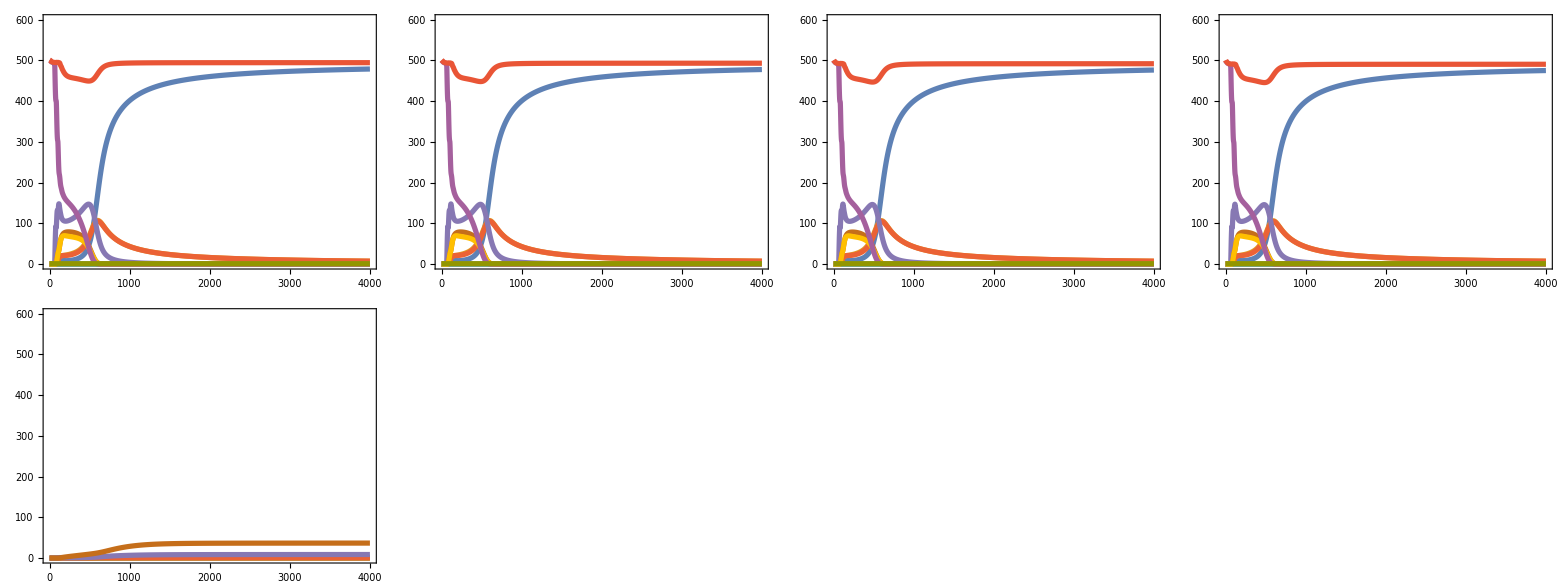

```mathematica
{
{PlotPopulationDynamicsFemales[rawData[[1,1]]],PlotPopulationDynamicsFemales[rawData[[1,2]]]},
{PlotPopulationDynamicsFemales[rawData[[2,1]]],PlotPopulationDynamicsFemales[rawData[[2,2]]]},
{PlotPopulationDynamicsFemales[rawData[[3,1]]],PlotPopulationDynamicsFemales[rawData[[3,2]]]},
{PlotPopulationDynamicsFemales[rawData[[4,1]]],PlotPopulationDynamicsFemales[rawData[[4,2]]]}
}//Transpose//Grid
```

## Translocations

```mathematica
SetDirectory[NotebookDirectory[]];
folders={"05_20_0025","05_20_0030","05_20_0035","05_20_0040"};
rawData=Table[
fileNames=FileNames["*.csv",Directory[]<>"/DARPAScenariosTranslocationsMigration/"<>i<>"/"];
labels=Import[fileNames[[1]]][[1,2;;All]];
(Import[#][[2;;All,2;;All]]&)/@fileNames
,{i,folders}];
```

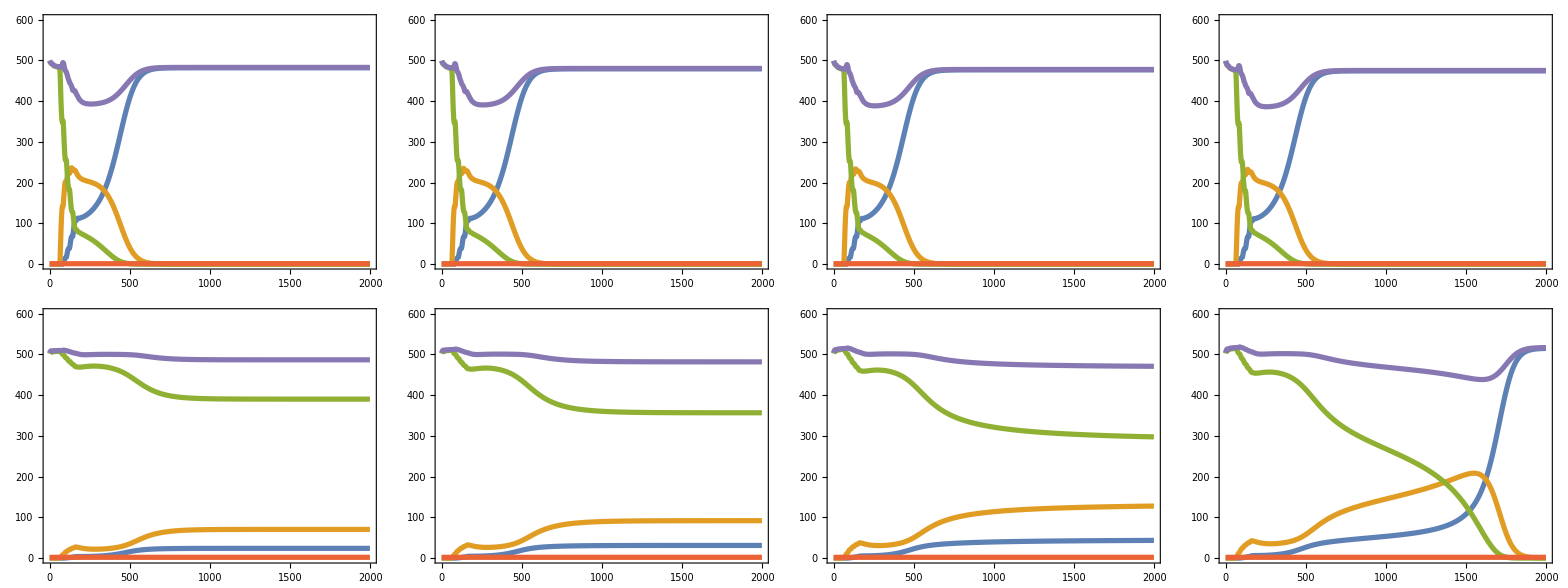

```mathematica
{
{PlotPopulationDynamicsFemales[rawData[[1,1]]],PlotPopulationDynamicsFemales[rawData[[1,2]]]},
{PlotPopulationDynamicsFemales[rawData[[2,1]]],PlotPopulationDynamicsFemales[rawData[[2,2]]]},
{PlotPopulationDynamicsFemales[rawData[[3,1]]],PlotPopulationDynamicsFemales[rawData[[3,2]]]},
{PlotPopulationDynamicsFemales[rawData[[4,1]]],PlotPopulationDynamicsFemales[rawData[[4,2]]]}
}//Transpose//Grid
```